```mathematica
malteseCrossArm1=(2x+y>=0 && 2x-y<=0) &&( 1/2x+y-2<=0 ||-1/2x+y-2<=0 )/.{x:>X, y->Y}/.{X:>x+y, Y:>y-x};
malteseCrossArm2=(2x+y<=0 && 2x-y>=0)&&( 1/2x+y+2>=0 ||-1/2x+y+2>=0 )/.{x:>X, y->Y}/.{X:>x+y, Y:>y-x};
malteseCrossArm3=(x+2 y≥0&&-x+2 y≤0&&(-2+x+y/2≤0||-2+x-y/2≤0))/.{x:>X, y->Y}/.{X:>x+y, Y:>y-x};
malteseCrossArm4=(x+2 y≤0&&-x+2 y≥0&&(2+x+y/2≥0||2+x-y/2≥0))/.{x:>X, y->Y}/.{X:>x+y, Y:>y-x};
```

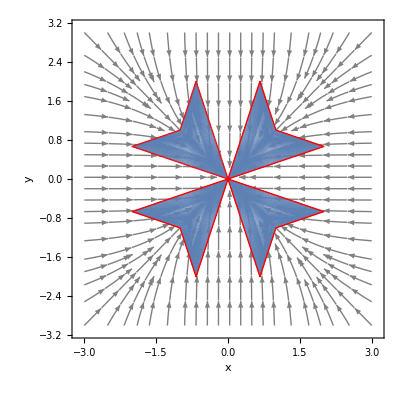

```mathematica
vf={-x^3, -y^3};
malteseCross=malteseCrossArm1 ||malteseCrossArm2 || malteseCrossArm3 || malteseCrossArm4;
R1=ImplicitRegion[malteseCross,{x,y}];

Show[
(* RegionPlot[x^2+y^2≤1, {x,-3,3},{y,-3,3}],*)
StreamPlot[vf,{x,-3,3},{y,-3,3},
 StreamStyle->Gray,
FrameLabel->{
Style[TraditionalForm[x],18, Black], 
Style[TraditionalForm[y],18, Black]},
LabelStyle->{FontFamily->"Source Serif Pro"},
 FrameTicks->Automatic,
 PlotRangePadding->0],
RegionPlot[BoundaryDiscretizeRegion[R1,MaxCellMeasure->{"Length"->0.02}], 
BoundaryStyle->{Thick, Red}
]
]
```

```mathematica
ES`ContinuousInvariantQ[malteseCross,vf, {x,y},True]//Timing
```

{144.422,True}

```mathematica
LZZ`ContinuousInvariantQ[malteseCross,vf, {x,y},True]//Timing
```

$Aborted